```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="English";
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"];
```

# PS1 - Dynamical Systems // Physics Institute UdeA // 2017-1 Juan Esteban Aristizábal Zuluaga Last update: Apr 1st 2017

## P. I

2.2.4	 ẋ=exp(-x)sin(x)

```mathematica
f[x_]:=Exp[-x]*Sin[x]
```

Fixed points :

```mathematica
fp=Reduce[f[x]==0,x ]
```

C[1]∈Integers&&(x==2 π C[1]||x==π+2 π C[1])

The number of fixed points is ifinite. Thus, stable and unstable fixed points are alternated. 

Linear stability analysis:

```mathematica
D[f[x],x]/.x->ConditionalExpression[(2*n+1)*π,n∈ℤ]
```

ConditionalExpression[ⅇ^(-(1+2 n) π) Cos[(1+2 n) π]-ⅇ^(-(1+2 n) π) Sin[(1+2 n) π],n∈ℤ]

The fixed points of the form  x^*= (2n+1)π   are stable    ((ⅆ ẋ)/ⅆx|_(x=(2n+1)π)<0)

```mathematica
D[f[x],x]/.x->ConditionalExpression[2n π,n∈ℤ]
```

ConditionalExpression[ⅇ^(-2 n π) Cos[2 n π]-ⅇ^(-2 n π) Sin[2 n π],n∈ℤ]

The fixed points of the form x* = 2nπ   are unstable,  ((ⅆ ẋ)/ⅆx|_(x=2n π)>0)

The figure shows the flow on the line, stable fixed points –black–, and unstable fixed points –red–

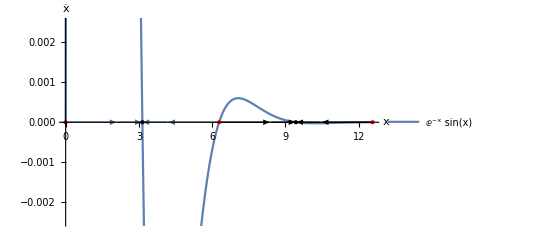

```mathematica
a=
Plot[
{f[x]},{x,0,4*Pi},
PlotRange->Full,
AxesLabel->{"x","ẋ"},
PlotLegends->{{f[x]}}
];

b=
StreamPlot[
{f[x],0},{x,0,4*π},{y,-0.5,0.5},StreamPoints->{{{{0,0},Black},{{2*Pi,0},Black},{{2.1*Pi,0},Black},{{-0.5*Pi,0},Black},{{3.5*Pi,0},Black}}},
StreamScale->Large
];

c=
ListPlot[
{{0,0},{2*π,0},{4*Pi,0}},
PlotStyle->{Red,PointSize[Large]}
];

d=
ListPlot[
{{π,0},{3*π,0}},
PlotStyle->{Black,PointSize[Large]}
];
Show[a,b,c,d,PlotRange-> {-0.0025,0.0025},AxesLabel->{"x","ẋ"},Axes->{True,True}]
```

```mathematica
CP[y_,i_]:=NDSolve[{y==x'[t],x[0.0]==i},x[t],{t,0,1000},Method->"Automatic"];
sol=Table[Evaluate[x[t]/.CP[f[x[t]],i]],{i,-1.99*Pi,1.99*Pi,Pi*0.24}];
```

NDSolve::ndinnt: Initial condition i is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{ⅇ^(-x[«1»]) Sin[x[t]]==x'[t],x[0.]==i},x[t],{t,0,1000},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Some solutions shown at different time scales:

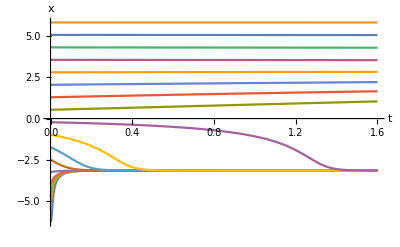

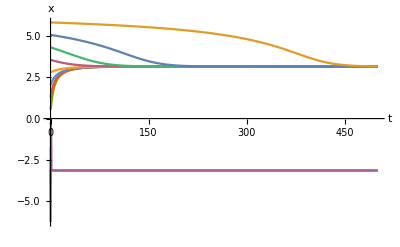

```mathematica
Plot[sol, {t,0,1.6},AxesLabel->{t,x}]
Plot[sol, {t,0,500},AxesLabel->{t,x}]
```

2.2.3	 ẋ=x(1-x^2)

```mathematica
g[x_]:=x(1-x^2)
```

Fixed points:

```mathematica
pf=Solve[g[x]==0,x]
```

{{x→-1},{x→0},{x→1}}

Linear stability analysis:

```mathematica
g'[x]/.pf
```

{-2,1,-2}

Fixed points x^*=±1 are stable and f.p. x^*=0 is unstable

Vector field on the line:

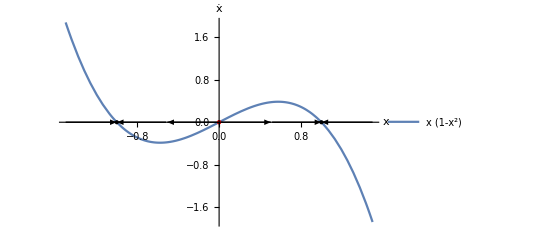

```mathematica
a1=
Plot[
g[x],{x,-1.5,1.5},
AxesLabel->{"x","ẋ"},
Axes->{True,True},
PlotLegends->{{g[x]}}
];

b1=
StreamPlot[
{g[x],0},{x,-1.5,1.5},{y,-2,2},
StreamPoints->{{{{-1.3,0},Black},{{-0.5,0},Black},{{0.5,0},Black},{{1.3,0},Black}}},
StreamScale->Medium
];

c1=
ListPlot[
{{0,0}},
PlotStyle->{Red,PointSize[Large]}
];

d1=
ListPlot[
{{-1,0},{1,0}},
PlotStyle->{Black,PointSize[Large]}
];

Show[a1,b1,c1,d1,Axes->{True,True},AxesLabel->{"x","ẋ"}]
```

Some solutions to the D.S.

NDSolve::ndinnt: Initial condition i is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x[t] (1-Power[«2»])==x'[t],x[0.]==i},x[t],{t,0,1000},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

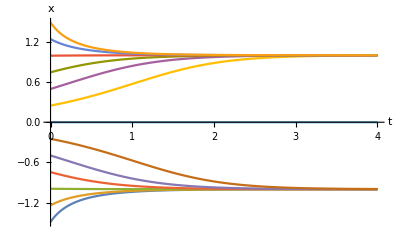

```mathematica
sol1=Table[Evaluate[x[t]/.CP[g[x[t]],i]],{i,-1.49,1.49,1.49/6.}];
Plot[sol1,{t,0,4},AxesLabel->{t,x}]
```

2.2.7    ẋ=exp(x)-cos(x)

```mathematica
f2[x_]:=Exp[x]-Cos[x]
```

Its not easy to find the fixed points of this dynamical system. However, we can infer  that if  x <<-1 , then ẋ→-cos(x) ,  thus x^*→ (-2 n +1)π/2 , n∈ℕ. And, taking into account that ⅇ^0=1, cos(0)=1 and ⅇ^x is an increasing function, it can be concluded that there are no fixed points for x>0 and there’s a fixed point at x=0. 
Graphically, we need to find the intersections between  cos x and ⅇ^x :

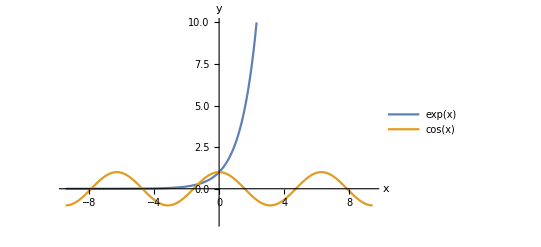

```mathematica
Plot[{Exp[x],Cos[x]},{x,-3*Pi,3*Pi},PlotRange-> {Full,{-2,10}},PlotLegends->"Expressions",AxesLabel->{x,"y"}]
```

Linear stability analysis

```mathematica
{xf21,xf22,xf23}=x/.NSolve[f2[x]==0 &&  -2Pi<x<1, x, Reals]
```

{-4.72129,-1.2927,0.}

The fixed points found over the interval -2π < x < 1  were x* ≈ - 4.72129 ≈ -3π/2,  x* ≈ -1.29269 and x* = 0.

Now, let’s see how are the (ⅆ ẋ)/ⅆx|_(x = x^*) values

```mathematica
f2'[x]/.x->{xf21,xf22,xf23}
```

{1.00886,-0.687049,1.}

From the figures above it is inferred that the fixed points x^* = {-4.7212927,-1.29269571,0}  are, respectively, unstable, stable and unstable. Notice what happens with the fixed ponts that tend to be x^*→ -(2 n +1)π/2 , n∈ℕ. It was said that if   x <<-1 , then ẋ→-cos(x). Thus, it is expected that the stability of the mentioned fixed points with the mentioned condition is the same as those fixed points of the dynamical system ẋ=-cos(x)
In fact, the the fixed points –of our D.S.– of the form x^*≈(-4n+1) π 2   n ∈ ℕ  are unestable ( f2'[x] > 0)  and those of the form x^*≈(-4n+3)π/2   n ∈ ℕ are stable ( f2’[x] < 0):

```mathematica
f2'[x]/.x->{-13π/2,-11π/2,-9π/2,-7π/2,-5π/2,-3π/2}
```

{-1+ⅇ^(-13 π/2),1+ⅇ^(-11 π/2),-1+ⅇ^(-9 π/2),1+ⅇ^(-7 π/2),-1+ⅇ^(-5 π/2),1+ⅇ^(-3 π/2)}

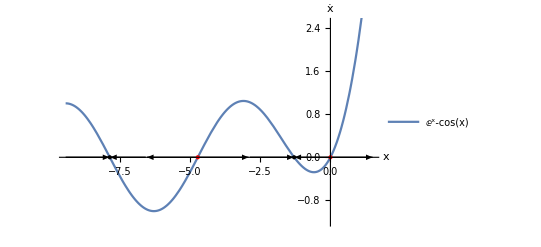

```mathematica
a2=
Plot[
{f2[x]},{x,-3π,π/2},
Axes->{True,True},
AxesLabel->{"x","ẋ"},
PlotLegends->{{f2[x]}}
];

b2=
StreamPlot[
{f2[x],0},{x,-3π,3/2},{y,-1,3},
StreamPoints->{{{{-5.0,0},Black},{{-4.1,0},Black},{{-0.5,0},Black},{{0.5,0},Black},{{-5*π/2-0.2,0},Black}}},
StreamScale->Large
];

c2=
ListPlot[
{{-4.7212927,0},{0,0}},
PlotStyle->{Red,PointSize[Large]}
];

d2=
ListPlot[
{{-1.2926,0},{-5*Pi/2,0}},
PlotStyle->{Black,PointSize[Large]}
];
Show[a2,b2,c2,d2,AxesLabel->{"x","ẋ"},Axes->{True,True},PlotRange-> {{-3*Pi,3/2},{-1.2,2.5}}]
```

```mathematica
sol2=Table[Evaluate[x[t]/.CP[f2[x[t]],i]],{i,-6.9π/2,0,π/4}];
sol22=Table[Evaluate[x[t]/.CP[f2[x[t]],i]],{i,0.1,0.11,0.07}];
```

NDSolve::ndinnt: Initial condition i is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{ⅇ^x[t]-Cos[x[«1»]]==x'[t],x[0.]==i},x[t],{t,0,1000},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition i is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{ⅇ^x[t]-Cos[x[«1»]]==x'[t],x[0.]==i},x[t],{t,0,1000},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsz: At t == 2.05084, step size is effectively zero; singularity or stiff system suspected.

Some solutions for x(0)<0  and a solution for x(0)>0
Note that the solution for x(0)>0 diverges because there are no fixed points for x>0 and x^*=0 is unstable:

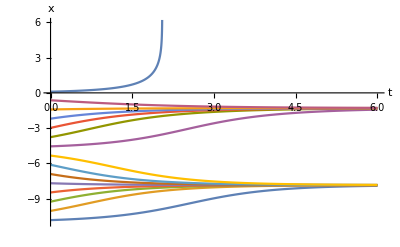

```mathematica
zz=Plot[sol2,{t,0,6},AxesLabel->{t,x}];
zzz=Plot[sol22,{t,0,2.4},AxesLabel->{t,x}];
Show[zz,zzz, PlotRange-> {-11,6}]
```

## P. II

2.2.8

Ya se vio que el sistema ẋ = x^2 presenta un punto semistable en x = 0. Una ecuación candidata a ser solución al problema es un polinomio. Intentemos con uno de grado 6. La idea será encontrar los coeficientes del polinomio para los cuales se cumplen las condiciones mostradas en el campo vectorial sobre la recta real del ejercicio. Se considerará  ẋ=f3(x) donde f(x) es la solución al problema.

```mathematica
f3[x_,a_,b_,c_,d_,e_]:=a*x^6+b*x^4+c*x^3+d*x^2+e
```

Algunas de las condiciones que se necesitan para que el SD ẋ=f3(x) cumpla con el diagrama de fase son:  f3(-1) = f(0) = f(2) = 0 = f3 ’ (-1).  Nótese que estas son algunas de las condiciones, pero no todas.

```mathematica
pol=Solve[{(f3[x,a0,b0,c0,d0,e0]/.x->-1)==0,(D[f3[x,a0,b0,c0,d0,e0],{x,1}]/.x->-1)==0,(f3[x,a0,b0,c0,d0,e0]/.x->2)==0,(f3[x,a0,b0,c0,d0,e0]/.x->0)==0},{a0,b0,c0,d0,e0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b0→-3 a0,c0→-2 a0,d0→0,e0→0}}

```mathematica
Clear[f3]
```

Tomando  a = 3 en  f3(x) y las soluciones dadas por ‘pol’ se tiene que f3 queda

```mathematica
f3[x_]:=x^6-3x^4-2x^3
```

Se corrobora que las condiciones dadas se cumplen y en efecto,

```mathematica
f3[-1]
f3[0]
f3[2]
f3'[-1]
```

0

0

0

«1 more identical outputs»

Además, se tiene que

```mathematica
f3[-2]>0
f3[-0.5]>0
f3[1]<0
f3[3]>0
```

True

True

True

«1 more identical outputs»

Y como los únicos valores de x* son los deseados: x* = {-1, 0, 2} y nuestra función es suave, se garantiza (junto con las otras condiciones impuestas) que la función es mayor que cero para x ∈ (-inf,-1)U(-1,0)U(2,inf)   y menor que cero para x ∈  (0,2)

```mathematica
Solve[f3[x]==0,x]
```

{{x→-1},{x→-1},{x→0},{x→0},{x→0},{x→2}}

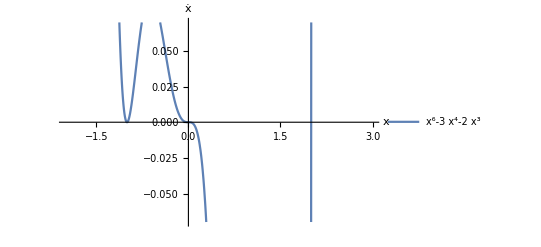

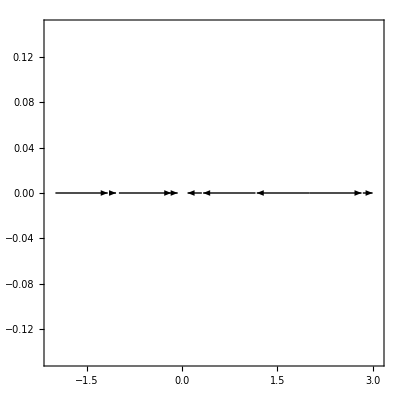

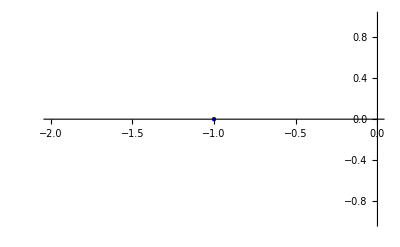

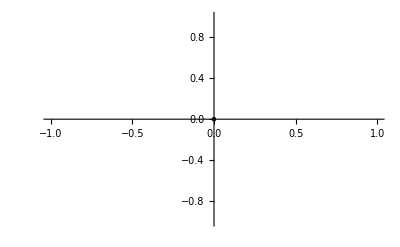

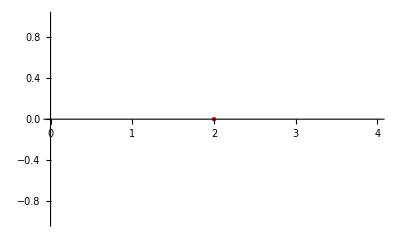

```mathematica
a3=Plot[{f3[x]},{x,-2,3},PlotRange->{-0.07,0.07},Axes->{True,True},AxesLabel->{"x","ẋ"},PlotLegends->{{f3[x]}}]
b3=StreamPlot[{f3[x],0},{x,-2,3},{y,-0.07,0.07},StreamScale->Large,StreamPoints->{{{{-1.5,0},Black},{{-.5,0},Black},{{1,0},Black},{{2.5,0},Black}}}]
c3=ListPlot[{{-1,0}},PlotStyle->{Blue,PointSize[Large]}]
d3=ListPlot[{{0,0}},PlotStyle->{Black,PointSize[Large]}]
e3=ListPlot[{{2,0}},PlotStyle->{Red,PointSize[Large]}]
```

La gráfica a continuación muestra el campo vectorial sobre la línea, punto fijo semi-estable en azul, punto fijo estable en negro y punto fijo inestable en rojo. Se puede ver que el SD ẋ=f3(x) cumple con las condiciones puestas en el problema.

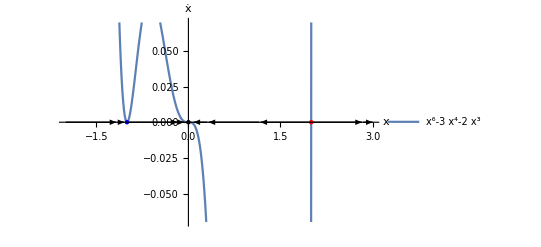

```mathematica
Show[a3,b3,c3,d3,e3,AxesLabel->{"x","ẋ"},Axes->{True,True}]
```

```mathematica
sol3=Table[Evaluate[x[t]/.CP[f3[x[t]],i]],{i,-1.91,1.91,.2}]
```

NDSolve::ndinnt: Initial condition i is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{-2 x[«1»]^3-3 x[«1»]^4+x[t]^6==x'[t],x[0.]==i},x[t],{t,0,1000},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]},{InterpolatingFunction[{{0., 1000.}}, <>][t]}}

A continuación, algunas soluciones del sistema dinámico para diferentes condiciones iniciales. Es claro que x* = -1 tiene un comportamiento extraño. Las soluciones que se encuentran por x<-1 , se acercan al punto fijo, pero si se encuentran por -1<x<0 este punto (x* = -1) se alejan de él. Los puntos fijos se muestran con líneas a rayas.

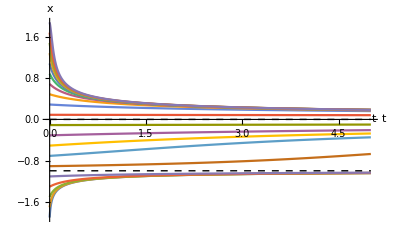

```mathematica
Plot[sol3,{t,0,5},AxesLabel->{"t","x"},Axes->{False,True},Epilog->{{Dashed,Line[{{0,-1},{5,-1}}]},{Dashed,Line[{{0,0},{5,0}}]},{Dashed,Line[{{0,2},{5,2}}]},Text["t",{5.05,0}]}]
```

2.2.10

a)	 ẋ = 0

b)	 ẋ = sin(π x)
	    Verificando las raíces:

```mathematica
f4[x_]:= Sin[π*x]
```

```mathematica
pf4=Reduce[{f4[x]==0},x]
```

C[1]∈Integers&&(x==2 C[1]||x==(π+2 π C[1])/π)

En efecto, si se mira con detalle, los puntos fijos del sistema son los n ∈ ℤ. Gráficamente:

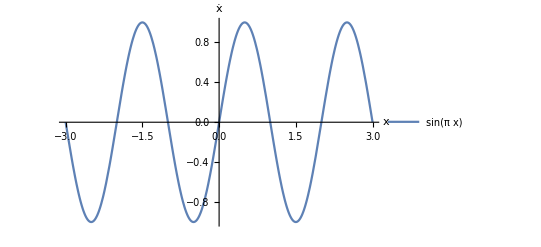

```mathematica
Plot[f4[x],{x,-3,3},Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{{f4[x]}}]
```

Es fácil ver que los puntos fijos n impares son estables y los n pares son inestables. Esto se logra viendo si la pendiente de la función en ese x* es positiva o negativa.

c)	No es posible tener un sistema con únicamente 3 puntos fijos estables, ya que habrá 2 o más puntos fijos del mismo tipo seguidos (estable o inestable) y no habrá entre ellos otro punto fijo del otro tipo (inestable o estable)

d)	 ẋ = sin(x)-2

Como se puede ver gráficamente, sin(x) ≠ 2  ∀ x ∈ ℝ. Esto es, el SD en cuestión no tiene puntos fijos.

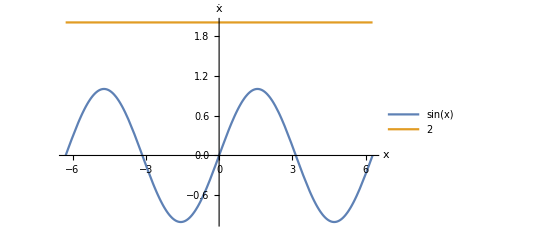

```mathematica
Plot[{{Sin[x]},{2}},{x,-2π,2π},PlotLegends->"Expressions",AxesLabel->{x,"ẋ"}]
```

e)	Cualquier polinomio con 100 raíces reales de multiplicidad 1. Es decir, de la forma f(x)=(x-x_1)(x-x_2)(x-x_3)...(x-x_99)(x-x_100), con x_i∈ ℝ, x_i≠x_j,      			                                 ∀i≠j ∈ {1,2,3...,100}

## P. III

2.3.3	 Crecimiento de tumores cancerígenos. Modelo:     ẋ=-a x ln(b x)  donde el número de células cancerígenas es proporcional a x(t)

```mathematica
f5[x_,ac_,bc_]:=-ac*x*Log[bc*x]
```

Veamos cómo se comporta la función cuando se varían los parámetros a y b. De ahora en adelante  a:=ac   y     b:=bc   (para que no haya confusión en el programa con otras variables definidas anteriormente)

```mathematica
Manipulate[Plot[{f5[x,ac,bc]},{x,0,3},AxesLabel->{"x","ẋ"},PlotLabel->"SD: Crecimiento de un tumor cancerígeno"],{ac,1,3},{bc,0.001,7}]
```

Es fácil darse cuenta –analíticamente– que el único punto fijo del sistema están en    x* = 1 / bc. 

El parámetro bc tiene unidades de [x^-1]. Con esto, y tomado ac>0 y bc>0 se tiene que el parámetro x* = 1/bc  es un punto fijo estable, ya que f5 ‘ (x=1/bc = 1/bc) < 0:

```mathematica
df5=D[f5[x,ac,bc],x]
```

-ac-ac Log[bc x]

```mathematica
df5/.x->1/bc
```

-ac

Con lo dicho y lo revisado anteriormente, se puede establecer que la cantidad  bc=1/k  es el recíproco de la “capacidad de carga” del sistema, k. Nótese que para valores grandes de bc (es decir, para valores pequeños de k), el punto fijo se acerca más a cero –esto se puede ver manipulando el parámetro en la gráfica anterior. 

Por otro lado, la cantidad ac es la que determina la rapidez con la que crece el número de células malignas. Es, por así decirlo, el parámetro que está relacionado con la ‘agresividad’ del tumor. Este parámetro tiene unidades  [1/t].

Por su parte, el punto x = 0 no puede ser punto fijo ya que habría una indeterminación con el logaritmo natural. Esto concuerda con lo establecido en el libro: el sistema es válido para valores de x lo suficientemente grandes.

La derivada de f5 es igual a cero cuando

```mathematica
xmax5=Solve[{df5==0},x]
```

{{x→1/(bc ⅇ)}}

Veamos si x = xmax5 es un máximo o un mínimo:

```mathematica
ddf5=D[df5,x]
ddf5/.x->1/(bc*E)
```

-ac/x

-ac bc ⅇ

Por criterio de la segunda derivada ( como f5 ’’ (xmax5) < 0  →  f5 (xmax5) es cóncava hacia abajo),  x = xmax5 es un máximo

Además, f5 (xmax5) = max5

```mathematica
max5=f5[1/(bc*E),ac,bc]
```

ac/(bc ⅇ)

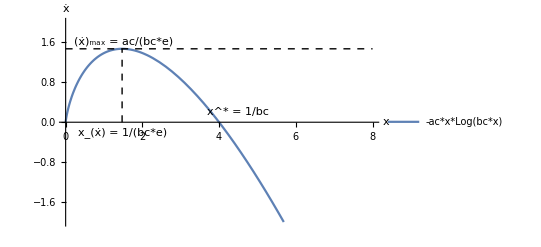

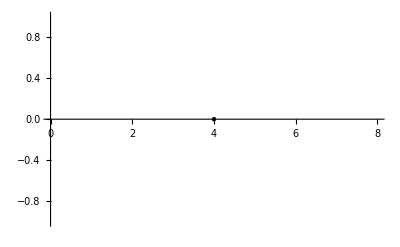

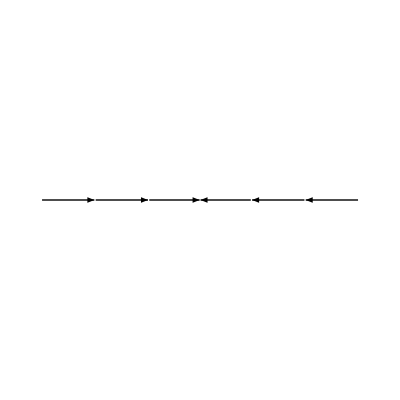

```mathematica
a5=Plot[f5[x,1,0.25],{x,0,8},PlotRange->{-2,2}, Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{"-ac*x*Log(bc*x)"},Epilog->{{Dashed,Line[{{0,1./(0.25*E)},{8,1./(0.25*E)}}]},{Dashed,Line[{{1./(0.25*E),0},{1./(0.25*E),1./(0.25*E)}}]},Text["(ẋ)_max = ac/(bc*e)",{1.5,(1./(0.25*E))+0.15}],Text["x_(ẋ) = 1/(bc*e)",{(1./(0.25*E)),-0.2}],Text["x^* = 1/bc",{4.5,0.2}]},Ticks->None]
b5=ListPlot[{{1/0.25,0}},PlotStyle->{Black,PointSize[Large]},Ticks->None]
c5=StreamPlot[{f5[x,0.4,0.25],0},{x,0,8},{y,-2,2},StreamPoints->{{{{2,0},Black},{{6,0},Black}}},StreamScale->Large,Ticks->None,Frame->None]
```

A continuación se muestra el campo vectorial y el punto fijo estable del sistema

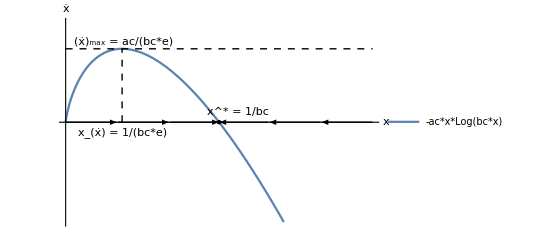

```mathematica
Show[a5,b5,c5,Ticks->False]
```

```mathematica
CP2[y_,i_,b_]:=NDSolve[{y[x[t],i,b]==x'[t],x[0.0]==0.01},x[t],{t,0,100},Method->"Automatic"]
```

```mathematica
sol5=Table[Evaluate[x[t]/.CP2[f5,i,0.25]],{i,0.5,1.25,.25}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{-i Log[0.25 x[«1»]] x[t]==x'[t],x[0.]==0.01},x[t],{t,0,100},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{InterpolatingFunction[{{0., 100.}}, <>][t]},{InterpolatingFunction[{{0., 100.}}, <>][t]},{InterpolatingFunction[{{0., 100.}}, <>][t]},{InterpolatingFunction[{{0., 100.}}, <>][t]}}

La siguiente figura muestra algunas soluciones para el sistema dinámico, para las mismas condiciones iniciales pero diferentes valores de ac.

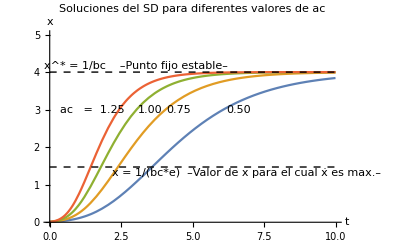

```mathematica
e5=Plot[sol5,{t,0,10},PlotRange->{0,5},PlotLegends->{{f5[x,ac,0.25]}},AxesLabel->{"t","x"},Axes->True,Ticks->None,Epilog->{Text["ac   =  1.25",{1.5,3}],Text["1.00",{3.5,3}],Text["0.75",{4.5,3}],Text["0.50",{6.6,3}],Text[Style["x^* = 1/bc    –Punto fijo estable–",Medium],{3,4.15}],Text["x = 1/(bc*e)  –Valor de x para el cual ẋ es max.–",{6.9,1.3}],{Dashed,Line[{{0,4},{10,4}}]},{Dashed,Line[{{0,1/(0.25*E)},{10,1/(0.25*E)}}]}},PlotLabel->"Soluciones del SD para diferentes valores de ac"]
```

Nótese que a medida que el parámetro ac crece, el tumor se acerca a su tamaño fijo en un tiempo mucho más corto. De alguna manera, se puede decir que es un tumor más difícil de combatir con tratamientos ya que hay menos tiempo para actuar y contrarrestar la enfermedad.

## P. IV

2.4.4    ẋ=x^2(6-x)

Veamos cuáles son los puntos fijos del sistema:

```mathematica
f6[x_]:=x^2*(6-x)
```

```mathematica
Solve[{f6[x]==0},x]
```

{{x→0},{x→0},{x→6}}

Los puntos fijos del sistema se dan entonces en x* = 0  y  x* =  6

Para saber si son puntos fijos estables o inestables, calculemos primero cuánto vale la derivada de ẋ=f6(x) en los valores de x*:

```mathematica
df6=D[f6[x],x]
```

2 (6-x) x-x^2

```mathematica
df6/.x->{0,6}
```

{0,-36}

Para x* = 0, f6 ‘ (x*) = 0, por lo que el criterio de estabilidad lineal no es concluyente. 

Por otro lado, para el punto fijo x* = 6,  f6 ‘ (x*)  = -36 < 0; y según el criterio de estabilidad lineal, este punto fijo es estable.

Analicemos el diagrama de fase del punto fijo x* = 0 con el método gráfico para determinar si es inestable o semi-estable. Ya es imposible que sea estable, dado que x* = 0 y x* = 6 son ls únicos puntos fijos del sistema y x* = 6 es estable –recordando que no es posible que dos puntos fijos estables (o semiestables) estén seguidos uno del otro, sin que exista otro punto fijo  en medio de ellos.

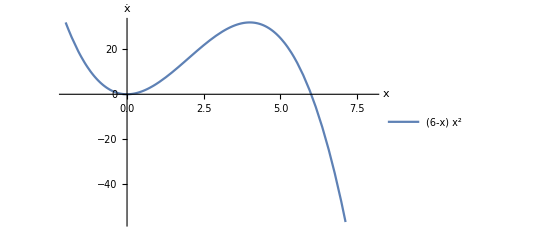

```mathematica
a6=Plot[f6[x],{x,-2,8},Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{{f6[x]}}]
```

Como se puede observar en gráfico ẋ vs x, el punto fijo x* = 0 es semi-estable, dado que la función f6(x) no cambia de signo en las vecindades de x*=0. Para las soluciones x(t) que se acercan por la izquierda de x*=0, el punto fijo se comporta como estable y para las soluciones que están a la derecha de x*=0, el punto fijo se comporta como inestable.

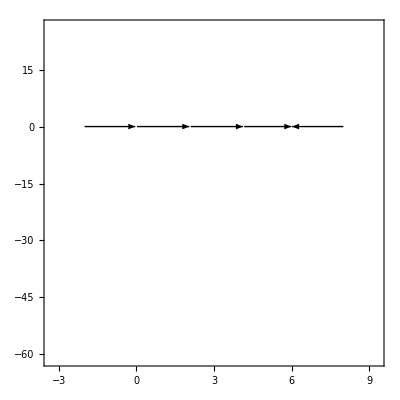

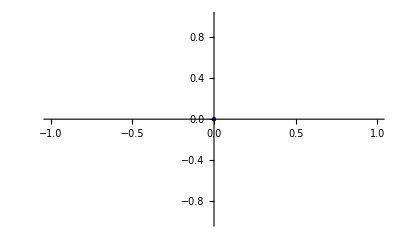

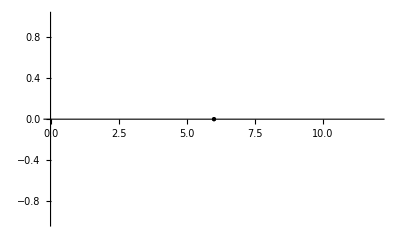

```mathematica
b6=StreamPlot[{f6[x],0},{x,-2,8},{y,-60,25},StreamPoints->{{{{-2.,0.},Black},{{2.,0.},Black},{{7.5,0.},Black}}},StreamScale->Large]
c6=ListPlot[{{0,0}},PlotStyle->{Blue,PointSize[Large]}]
d6=ListPlot[{{6,0}},PlotStyle->{Black,PointSize[Large]}]
```

A continuación, el campo vectorial para el sistema, con sus respectivos puntos fijos (el estable, en negro; el semi-estable, en azul)

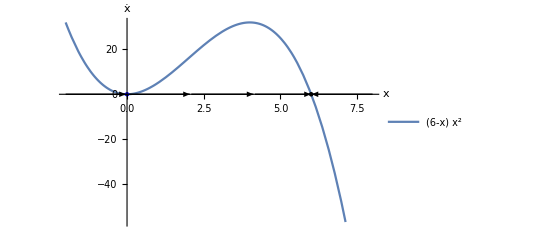

```mathematica
Show[a6,b6,c6,d6]
```

2.4.5    ẋ=1-exp(-x^2)

Puntos fijos del sistema:

```mathematica
f7[x_]:=1-Exp[-x^2]
```

```mathematica
Solve[{f7[x]==0,x ∈ Reals},x]
```

{{x→0},{x→0}}

El único punto fijo del sistema es x* = 0

Veamos si se puede aplicar el criterio de estabilidad lineal a este punto

```mathematica
f7'[0]
```

0

Como la derivada evaluada en el punto fijo es igual a cero, el criterio no es concluyente, por lo cual se recurre al método gráfico

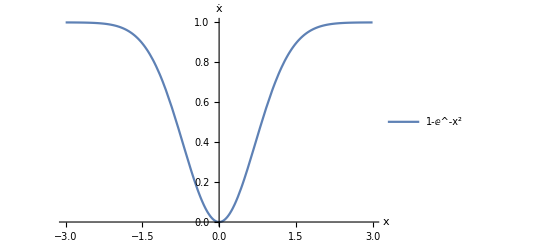

```mathematica
a7=Plot[f7[x],{x,-3,3},Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{{f7[x]}}]
```

De la gráfica es evidente que el único punto fijo del sistema, x* = 0, es semi-estable. Las soluciones que sus condiciones iniciales están dadas para x<0, se acercan al punto fijo; pero las que están dadas para x>0 se alejan del mismo.

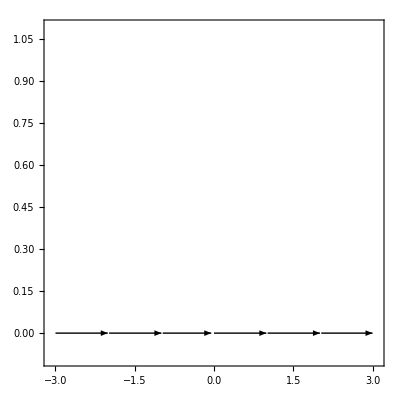

-Graphics-

```mathematica
b7=StreamPlot[{f7[x],0},{x,-3,3},{y,0,1},StreamPoints->{{{{-2,0},Black},{{2,0},Black}}},StreamScale->Large]
c7=ListPlot[{{0,0}},PlotStyle->{Black,PointSize[Large]}]
```

Así queda el campo vectorial del S.D. :

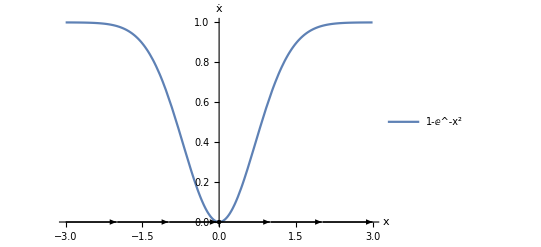

```mathematica
Show[a7,b7,c7]
```

2.4.7    ẋ=x(aa-x^2)

```mathematica
f8[x_,aa_]:=x*(aa-x^2)
```

Puntos fijos del sistmea:

```mathematica
pf8=Solve[{x*(aa-x^2)==0},x]
```

{{x→0},{x→-√aa},{x→√aa}}

Para aa > 0 :

Los puntos fijos del sistema serían los consignados en pf7, ya que no existen indeterminaciones sobre los reales para esos puntos fijos.

Puntos fijos:

```mathematica
pf8
```

{{x→0},{x→-√aa},{x→√aa}}

Analicemos la estabilidad de cada punto fijo:

```mathematica
df8=D[x*(aa-x^2),x]/.x->{0,-√aa,√aa}
```

{aa,-2 aa,-2 aa}

Por criterio de estabilidad lineal, el punto fijo x^*=0 es inestable; y los puntos fijos x^*=±√aa son estables.

```mathematica
f81[x_]:=f8[x,1]
```

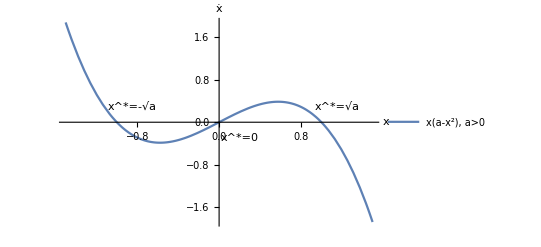

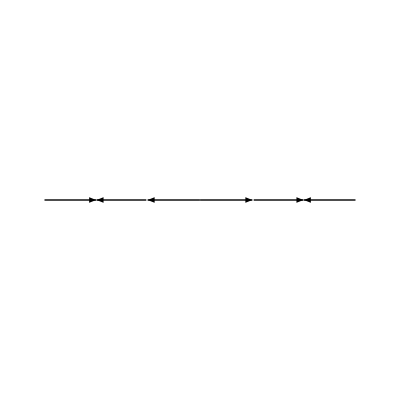

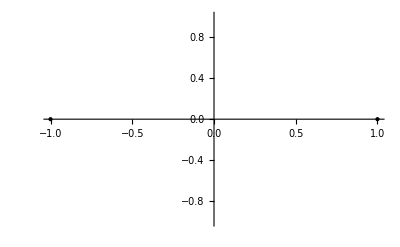

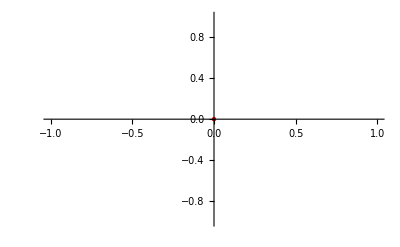

```mathematica
a81=Plot[f81[x],{x,-1.5,1.5},Axes->True,AxesLabel->{"x","ẋ"},Ticks->None,PlotLegends->{{"x(a-x^2), a>0"}},Epilog->{Text[Style["x^*=-√a",Medium],{-0.85,0.3}],Text[Style["x^*=√a",Medium],{1.15,0.3}],Text[Style["x^*=0",Medium],{0.2,-0.3}]}]
b81=StreamPlot[{f81[x],0},{x,-1.5,1.5},{y,-2,2},StreamPoints->{{{{-1.25,0},Black},{{1.25,0},Black},{{.25,0},Black},{{-.25,0},Black}}},StreamScale->Large,Frame->False]
c81=ListPlot[{{-1,0},{1,0}},PlotStyle->{Black,PointSize[Large]},Ticks->None]
d81=ListPlot[{{0,0}},PlotStyle->{Red,PointSize[Large]},Ticks->None]
```

Así queda el campo vectorial, con a > 0.

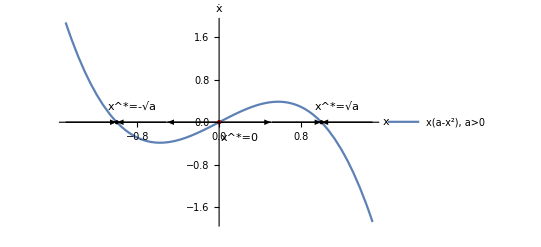

```mathematica
Show[a81,b81,c81,d81]
```

Para aa < 0 :

Recordemos los puntos fijos posibles en el caso general:

```mathematica
pf8
```

{{x→0},{x→-√aa},{x→√aa}}

Si se toma aa<0, es claro que el uúnico punto fijo sobre los reales sería x=0.
Analicemos la estabilidad del pinto fijo:

```mathematica
D[x*(aa-x^2),x]/.x->0
```

aa

y como aa < 0  (por hiótesis), entonces x^*=0 es un punto fijo estable

```mathematica
f82[x_]:=f8[x,-1]
```

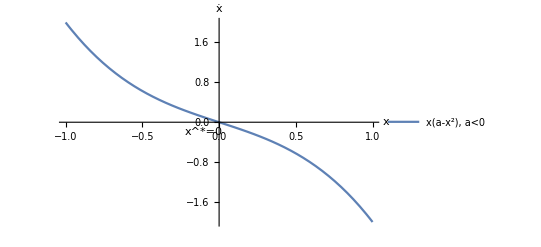

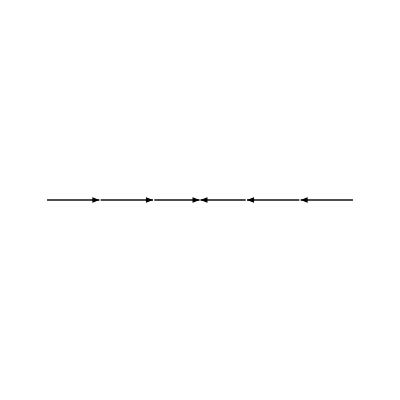

-Graphics-

```mathematica
a82=Plot[f82[x],{x,-1,1},Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{{"x(a-x^2), a<0"}},Ticks->None,Epilog->{Text[Style["x^*=0",Medium],{-0.1,-0.2}]}]
b82=StreamPlot[{f82[x],0},{x,-1,1},{y,-2,2},StreamPoints->{{{{0.5,0},Black},{{-0.5,0},Black}}},StreamScale->Large,Frame->False]
c82=ListPlot[{{0,0}},PlotStyle->{Black,PointSize[Large]},Ticks->None]
```

El campo vectorial del sistema queda:

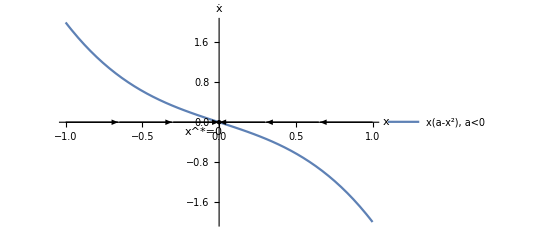

```mathematica
Show[a82,b82,c82]
```

Para aa = 0 :

El S.D. queda:

```mathematica
f83[x_]:=f8[x,0]
```

```mathematica
f83[x]
```

-x^3

ẋ=-x^3

El único punto fijo del sistema es x^*=0. Veamos si es posible analizarlo con el criterio de estabilidad lineal:

```mathematica
f83'[x]/.x->0
```

0

Como la derivada del S.D ẋ=f83 (x) evaluada en x^*=0 es igual a cero, entonces el criterio no es concluyente. Se acude al método gráfico para analizar la estabilidad del sistema:

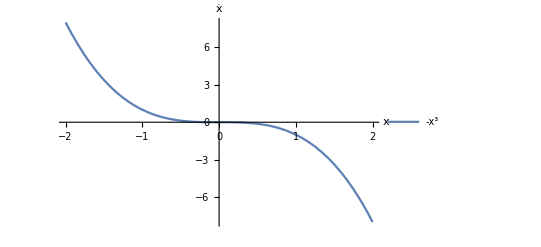

```mathematica
a83=Plot[f83[x],{x,-2,2},Axes->True,AxesLabel->{"x","ẋ"},PlotLegends->{{f83[x]}}]
```

Claramente, del gráfico se puede concluir que el único punto fijo x^*=0 es estable.

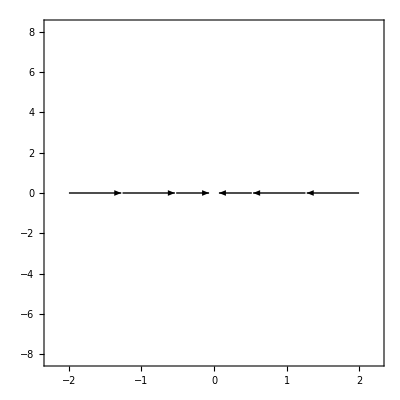

-Graphics-

```mathematica
b83=StreamPlot[{f83[x],0},{x,-2,2},{y,-8,8},StreamPoints->{{{{-1,0},Black},{{1,0},Black}}},StreamScale->Large]
c83=ListPlot[{{0,0}},PlotStyle->{Black,PointSize[Large]}]
```

A continuación el campo vectorial del S.D.

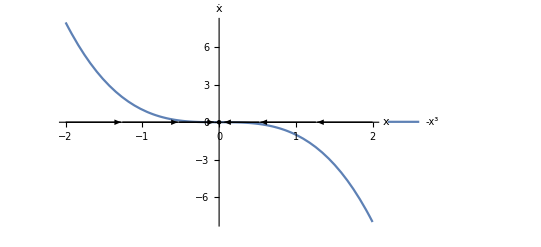

```mathematica
Show[a83,b83,c83]
```

## P. V

2.8.6    ẋ=x+ ⅇ^-x

```mathematica
f9[x_]:=x+Exp[-x]
```

a) Solución

```mathematica
sol9=NDSolve[{f9[x[t]]==x'[t],x[0.0]==0.},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

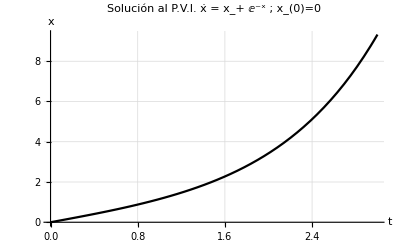

```mathematica
Plot[Evaluate[x[t]/.sol9],{t,0,3},PlotStyle->Black,PlotRange->Full,AxesLabel->{"t","x"},GridLines->Automatic,PlotLabel->"Solución al P.V.I. ẋ = x_+ ⅇ^-x   ;   x_(0)=0"]
```

b)  Definiedo (ẋ)_1≡x_1+1  y (ẋ)_2≡1  , y considerando el problema de valor inicial  x_2(0)=x_1(0)=x(0)=0 es fácil ver que para x≥0 se tiene que  ẋ≤(ẋ)_1. Ahora veamos que se cumple también que para x≥0 ,    (ẋ)_2≤ẋ. Esto es:

```mathematica
Reduce[{1≤x+Exp[-x]},x]
```

(x∈Reals&&-1+x≠0)||x==0||x==1

Ahora, podemos afirmar que para x≥0 se cumple que (ẋ)_2≤ẋ≤(ẋ)_1. Luego, se tiene que para x≥0 se cumplen (ẋ)_2,(ẋ)_1,ẋ≥0  y   (ⅆ(ẋ)_2)/(ⅆ x_2),(ⅆ(ẋ)_1)/(ⅆ x_1),(ⅆ ẋ)/ⅆx≥0 :

```mathematica
Reduce[{D[1,x]>=0,x∈Reals},x]
Reduce[{D[x+1,x]>=0,x∈Reals},x]
Reduce[{f9'[x]>=0,x∈Reals},x]
```

x∈Reals

x∈Reals

x≥0

Esto es, las funciones (ẋ)_1,(ẋ)_2,ẋ son no decrecientes y positivas para x≥0 y por tanto, las funciones x_1(t),x_2(t),x(t) son no decrecientes y no negativas para t≥0. Teniendo todo lo anterior en cuenta, se puede afirmar entonces que para el problema de valor inicial dado, x_2(t)≤x(t)≤x_1(t). Ahora encontremos x_2(1)=a   y  x_1(1)=b  de modo que a≤x(1)≤b. Es decir, acotemos x(1):

Para x_2(t), la integración de la E.D. es sencilla:   x_2(t) =t+C  ;  x_2(0)=0   →  C=0  →   x_2(t)=t  →  x_2(1)=a=1

Para x_1(t), la integración queda:   Log|(x_1(t)+1)C|=t     ;    x_1(0)=0    →   (x_1(t)+1)C= ⅇ^t  →   C=ⅇ^0=1 →   x_1(t)=ⅇ^t-1   →   x_1(1)=b=ⅇ-1

Así, se ha acotado el valor de x(1) :        1≤x(1)≤ⅇ-1

c) Ahora integremos la ecuación usando el método de Euler ẋ= f9(x) para hallar cuánto vale x(1).

```mathematica
x1=0.0
t1=0.0
dt1=1.0
err1=1.0
DT1={}
ERR1={}
X1={x1}
While[err1>(10^(-3)),
While[t1<1,
x1+=f9[x1]*dt1;
t1+=dt1
];
X1=Append[X1,x1];
DT1=Append[DT1,dt1];
err1=Abs[X1[[-1]]-X1[[-2]]];
ERR1=Append[ERR1,err1];
t1=0;
x1=0;
dt1=dt1*(10^(-1))
]
X1=Delete[X1,1]
ERR1=Delete[ERR1,1]
```

0.

0.

1.

1.

{}

{}

{0.}

{1.,1.12745,1.15084,1.15336,1.15376}

{0.127453,0.0233826,0.00252125,0.000400997}

El orden de magnitud del paso para que el cálculo de x(1) por el método de Euler sea correcto en 3 cifras significativas debe ser de    dt=10^-4 .   Además, el valor dado por este método es:

```mathematica
X1[[-1]]
```

1.15376

Es decir, x(1)≈1.153. El valor dado por la integración en “sol9” es:

```mathematica
sol9/.t->1
```

{{x[1]→1.15364}}

Lo que es congruente con el resultado dado por la solución con el método de Euler y las cotas dadas en el punto b)

d) Ahora usemos integración por el método de Runge Kutta 4 para el mismo S.D.

```mathematica
x1=0.0
t1=0.0
dt1=1.0
err1=1.0
DT11={}
ERR11={}
X11={x1}
While[err1>(10^(-5)),
While[t1<1,
k1=f9[x1]*dt1;
k2=f9[x1+0.5*k1]*dt1;
k3=f9[x1+0.5*k2]*dt1;
k4=f9[x1+k3]*dt1;
x1+=(1.0/6.0)*(k1+2*k2+2*k3+k4);
t1+=dt1
];
X11=Append[X11,x1];
DT11=Append[DT11,dt1];
err1=Abs[X11[[-1]]-X11[[-2]]];
ERR11=Append[ERR11,err1];
t1=0;
x1=0;
dt1=dt1*(10^(-1))
]
X11=Delete[X11,1]
ERR11=Delete[ERR11,1]
```

0.

0.

1.

1.

{}

{}

{0.}

{1.15361,1.15364,1.15364}

{0.0000329961,1.49072×10^-8}

En este caso, con un paso dt=1 el método de Runge Kutta 4 YA TIENE LA PRECISIÓN DESEADA (y más...). La precisión con un dt=0.1 es del orden de 10^-5 y con un dt=0.01 es del orden de 10^-8 –estos valores están consignados en el vector ERR11–. Los valores de x(1) dados por este método para los dt mencionados son, respectivamente,

```mathematica
X11[[1]]
X11[[2]]
X11[[3]]
```

1.15361

1.15364

1.15364

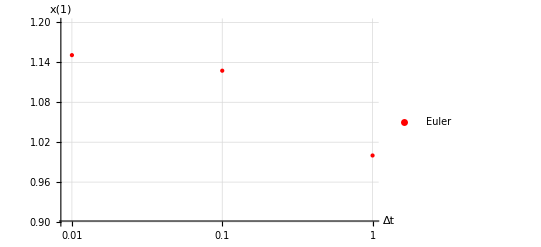

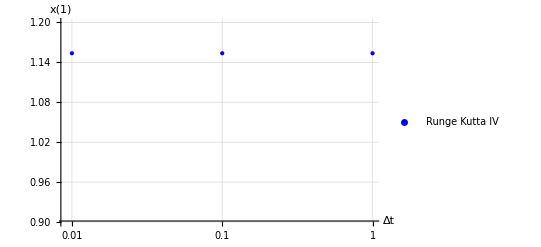

```mathematica
a10=ListLogLinearPlot[{{DT1[[1]],X1[[1]]},{DT1[[2]],X1[[2]]},{DT1[[3]],X1[[3]]}},PlotStyle->{Red,PointSize[Large]},PlotLegends->{{"Euler"}},AxesLabel->{"Δt","x(1)"},GridLines->Automatic,PlotRange->{.9,1.20}]
b10=ListLogLinearPlot[{{DT11[[1]],X11[[1]]},{DT11[[2]],X11[[2]]},{DT11[[3]],X11[[3]]}},PlotStyle->{Blue,PointSize[Large]},PlotLegends->{{"Runge Kutta IV"}},AxesLabel->{"Δt","x(1)"},GridLines->Automatic,PlotRange->{.9,1.20}]
```

Gráficamente se puede apreciar mejor la diferencia entre los dos métodos usados:

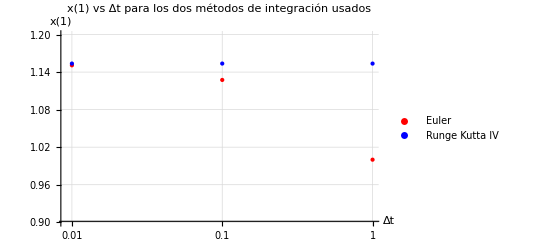

```mathematica
Show[a10,b10,PlotLabel->"x(1) vs Δt para los dos métodos de integración usados"]
```

Es claro que el método de Runge Kutta IV no necesita un Δt muy pequeño para dar un valor preciso de la integración deseada,  cuando se compara con el método de Euler.

La siguiente, para apreciar mejor el rango de acción del método Runge Kutta IV en este caso :

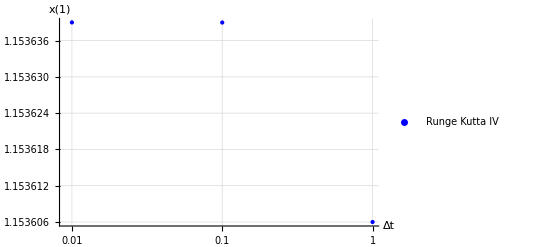

```mathematica
b10=ListLogLinearPlot[{{DT11[[1]],X11[[1]]},{DT11[[2]],X11[[2]]},{DT11[[3]],X11[[3]]}},PlotStyle->{Blue,PointSize[Large]},PlotLegends->{{"Runge Kutta IV"}},AxesLabel->{"Δt","x(1)"},GridLines->Automatic]
```

## P. VI

2.5.3.    ẋ=x(r+x^2)   ;   r>0

```mathematica
f11[x_,r_]:=x*(r+x^2)
```

Integrando :

```mathematica
Simplify[Integrate[1/f11[x,r],x]]
```

-(-2 Log[x]+Log[r+x^2])/(2 r)

Esto es, -2r t=Log(C(r/x^2+1))    ;   x(t_0)=x_0 ;   x_0≠0  
→   x(t)=±√((r*C)/(ⅇ^(-2r t) -    C))    ;    C=ⅇ^(-2r t_0)/(r/x_0^2+1)  
De lo anterior se deduce que x(t)→±∞  cuando  t→t_f  tal que
  ⅇ^(-2r t_f) -    C  = 0   
→   t_f=1/(-2r)Log(C)=1/(-2r)Log(ⅇ^(-2r t_0)/(r/x_0^2 + 1))  
→   t_f = t_0+1/(2r)Log(r/x_0^2 + 1)

En resumen, para cualquier condición inicial   x(t_0)=x_0 ;   x_0≠0, se tiene que  
 x(t)→±∞  cuando t  → t_f= t_0+1/(2r)Log(r/x_0^2 + 1) > 0   Esto es, x(t)→±∞ en un tiempo finito.